# Unit 2 · Mathematics as Data

## Trees, prefix notation, fair sampling and checked answers (Lample and Charton, 2019) — TensorNets units of learning, 2 of 4

© 2026 Computational Classnotes · CC BY-NC-SA 4.0

A neural net can learn to integrate if integration is written as translation: the problem is one sequence, its solution another. Lample and Charton (2019) trained a standard transformer this way. What was new was the data. This unit builds their data machinery: trees in prefix notation, counting and fair sampling of trees, three ways of making integration problems, and checking every answer. Evaluate the notebook from top to bottom; it takes about a minute. The write-up “Unit 2 · Mathematics as Data” has the same section numbers.

Before you start: choose Evaluation ▸ Quit Kernel ▸ Local.

## 1. Toolkit

Every function the unit uses. prefixOf writes a Wolfram expression as prefix tokens and fromPrefix reads them back (§3). nTrees[e, n] is the count D(e, n) of §4 and nBin its binary version; randomTree samples them uniformly (§5); decorate and randomExpr turn trees into expressions. bwd, fwd and ibpRound make integration data (§6); verifiedQ checks an answer by differentiating it (§7). The variable is Wolfram’s formal symbol \[FormalX], which shows as a dotted x and can never be given a value by accident.

```mathematica
(* id: 1b07eda0-f4a5-4e3d-a6f7-e18f32b9a015 · unit2_symbolic_data · cell 1 of 27 · updated 2026-11-24 06:52 UTC *)
arity = <|"add" -> 2, "sub" -> 2, "mul" -> 2, "div" -> 2, "pow" -> 2, "exp" -> 1, "log" -> 1, "sin" -> 1, "cos" -> 1|>;
ops = <|"add" -> Plus, "sub" -> Subtract, "mul" -> Times, "div" -> Divide, "pow" -> Power, "exp" -> Exp, "log" -> Log, "sin" -> Sin, "cos" -> Cos|>;
intTokens[n_Integer] := Join[{If[n >= 0, "INT+", "INT-"]}, Characters@IntegerString[Abs[n]]];
(* Wolfram expression -> prefix tokens; long sums and products become right-nested binary nodes; Exp[a] is E^a inside Wolfram *)
prefixOf[e_Integer] := intTokens[e];
prefixOf[Rational[p_, q_]] := Join[{"div"}, intTokens[p], intTokens[q]];
prefixOf[x] := {"x"};
prefixOf[E] := {"E"};
prefixOf[Power[E, a_]] := Prepend[prefixOf[a], "exp"];
prefixOf[(h : Plus | Times)[a_, b_, c__]] := Join[{If[h === Plus, "add", "mul"]}, prefixOf[a], prefixOf[h[b, c]]];
prefixOf[Plus[a_, b_]] := Join[{"add"}, prefixOf[a], prefixOf[b]];
prefixOf[Times[a_, b_]] := Join[{"mul"}, prefixOf[a], prefixOf[b]];
prefixOf[Power[a_, b_]] := Join[{"pow"}, prefixOf[a], prefixOf[b]];
prefixOf[(f : Log | Sin | Cos)[a_]] := Prepend[prefixOf[a], ToLowerCase@SymbolName[f]];
prefixOf[_] := {"<unk>"};
(* prefix tokens -> expression, reading left to right; $Failed unless the tokens are exactly one tree *)
fromPrefix[tokens_List] := Module[{pos = 1, rec, r},
   rec[] := Module[{t}, If[pos > Length[tokens], Throw[$Failed, tag]]; t = tokens[[pos++]];
     Which[KeyExistsQ[arity, t], ops[t] @@ Table[rec[], arity[t]],
      t === "x", x, t === "E", E,
      t === "INT+" || t === "INT-", Module[{ds = {}},
        While[pos <= Length[tokens] && StringMatchQ[tokens[[pos]], DigitCharacter], AppendTo[ds, tokens[[pos++]]]];
        If[ds === {}, Throw[$Failed, tag]]; If[t === "INT-", -1, 1] FromDigits[StringJoin[ds]]],
      True, Throw[$Failed, tag]]];
   r = Quiet@Catch[rec[], tag]; If[r === $Failed || pos <= Length[tokens], $Failed, r]];
validQ[tokens_List] := fromPrefix[tokens] =!= $Failed;
(* the counter of §3: how many subtrees are still owed after each token *)
owed[tokens_List] := Module[{keep = {}, inInt = False},       (* the digits after INT+ or INT- belong to that integer *)
   Do[If[! (inInt && StringMatchQ[t, DigitCharacter]), AppendTo[keep, t]];
    inInt = MemberQ[{"INT+", "INT-"}, t] || (inInt && StringMatchQ[t, DigitCharacter]), {t, tokens}];
   FoldList[#1 + Lookup[arity, #2, 0] - 1 &, 1, keep]];
(* counting (§4): e empty slots, n internal nodes still to place *)
nTrees[_, 0] = 1; nTrees[0, n_ /; n > 0] = 0;
nTrees[e_, n_] := nTrees[e, n] = nTrees[e - 1, n] + nTrees[e, n - 1] + nTrees[e + 1, n - 1];
nBin[_, 0] = 1; nBin[0, n_ /; n > 0] = 0;
nBin[e_, n_] := nBin[e, n] = nBin[e - 1, n] + nBin[e + 1, n - 1];
allTrees[0] = {{0}};
allTrees[n_] := allTrees[n] = Join[Prepend[#, 1] & /@ allTrees[n - 1],
    Flatten[Table[Join[{2}, l, r], {i, 0, n - 1}, {l, allTrees[i]}, {r, allTrees[n - 1 - i]}], 2]];
schroeder[0] = 1; schroeder[1] = 2;
schroeder[n_] := schroeder[n] = (3 (2 n - 1) schroeder[n - 1] - (n - 2) schroeder[n - 2])/(n + 1);
weight[t_List, {L_, p1_, p2_}] := L^Count[t, 0] p1^Count[t, 1] p2^Count[t, 2];
Eexpr[0, {L_, p1_, p2_}] := L; Eexpr[1, {L_, p1_, p2_}] := p1 L + p2 L^2;
Eexpr[n_, w : {L_, p1_, p2_}] := Eexpr[n, w] = ((p1 + 2 L p2) (2 n - 1) Eexpr[n - 1, w] - p1^2 (n - 2) Eexpr[n - 2, w])/(n + 1);
Eprinted[0, {L_, p1_, p2_}] := L; Eprinted[1, {L_, p1_, p2_}] := p1 L + p2 L^2;
Eprinted[n_, w : {L_, p1_, p2_}] := Eprinted[n, w] = ((p1 + 2 L p2) (2 n - 1) Eprinted[n - 1, w] - p1 (n - 2) Eprinted[n - 2, w])/(n + 1);
(* sampling (§5): Algorithm 2 (unary-binary) and Algorithm 1 (binary) of the paper's Appendix C *)
choices[e_, n_] := Flatten[Table[{{k, 1} -> nTrees[e - k, n - 1], {k, 2} -> nTrees[e - k + 1, n - 1]}, {k, 0, e - 1}], 1];
randomTree[n0_Integer] := Module[{e = 1, n = n0, ch, k, a, out = {}},
   While[n > 0, ch = choices[e, n]; {k, a} = RandomChoice[Values[ch] -> Keys[ch]];
    out = Join[out, ConstantArray[0, k], {a}]; e = If[a == 1, e - k, e - k + 1]; n--];
   Join[out, ConstantArray[0, e]]];
randomBinaryTree[n0_Integer] := Module[{e = 1, n = n0, ks, k, out = {}},
   While[n > 0, ks = Range[0, e - 1]; k = RandomChoice[(nBin[e - # + 1, n - 1] & /@ ks) -> ks];
    out = Join[out, ConstantArray[0, k], {2}]; e = e - k + 1; n--];
   Join[out, ConstantArray[0, e]]];
naiveTree[0] := {0};
naiveTree[n_Integer] := If[RandomReal[] < 0.45, With[{m = RandomInteger[{0, n - 1}]}, Join[{2}, naiveTree[m], naiveTree[n - 1 - m]]], Prepend[naiveTree[n - 1], 1]];
uniformP[samples_, all_] := Module[{c = Lookup[Counts[samples], all, 0], ex = Length[samples]/Length[all]},
   1 - CDF[ChiSquareDistribution[Length[all] - 1], Total[(c - ex)^2/ex]]];
decorate[t_List] := Flatten[Switch[#, 2, RandomChoice[{"add", "sub", "mul", "div"}], 1, RandomChoice[{"exp", "log", "sin", "cos"}],
      0, If[RandomReal[] < 0.5, "x", intTokens[RandomChoice[{-5, -4, -3, -2, -1, 1, 2, 3, 4, 5}]]]] & /@ t];
randomExpr[n_Integer] := fromPrefix[decorate[randomTree[n]]];
(* data (§6) and checking (§7) *)
goodQ[e_] := FreeQ[e, Complex | DirectedInfinity | Indeterminate | $Failed | Integrate] && ! FreeQ[e, x] &&
   With[{t = prefixOf[e]}, FreeQ[t, "<unk>"] && Length[t] <= 40];
bwd[] := Module[{f, df}, Do[f = randomExpr[RandomInteger[{1, 4}]];
    If[goodQ[f], df = TimeConstrained[Quiet@Simplify[D[f, x]], 1, $Failed]; If[goodQ[df], Return[{df, f}, Module]]], {300}]; $Failed];
fwd[] := Module[{f, F}, Do[f = randomExpr[RandomInteger[{1, 4}]];
    If[goodQ[f], F = TimeConstrained[Quiet@Integrate[f, x], 1, $Failed]; If[goodQ[F], Return[{f, F}, Module]]], {300}]; $Failed];
lookup[table_, p_] := Module[{r}, Do[r = Quiet@Simplify[p/q[[1]]];
    If[FreeQ[r, x] && FreeQ[r, Indeterminate | DirectedInfinity], Return[r q[[2]], Module]], {q, table}]; $Failed];
ibpRound[table_, pool_] := Module[{new = table, known},
   Do[If[F =!= G, known = lookup[new, Simplify[D[F, x] G]];
     If[known =!= $Failed, With[{p = Simplify[F D[G, x]], s = Simplify[F G - known]}, If[lookup[new, p] === $Failed, AppendTo[new, {p, s}]]]]],
    {F, pool}, {G, pool}]; new];
verifiedQ[problem_, tokens_List] := With[{F = fromPrefix[tokens]}, F =!= $Failed && TrueQ[Quiet@Simplify[D[F, x] - problem] === 0]];
(* drawing a prefix sequence as its tree *)
treeGraph[tokens_List] := Module[{pos = 0, edges = {}, rec},
   rec[] := Module[{me = ++pos, t = tokens[[pos]], k}, Do[k = rec[]; AppendTo[edges, me -> k], Lookup[arity, t, 0]]; me];
   rec[]; Graph[Range[Length[tokens]], edges, VertexLabels -> Table[i -> Placed[Style[tokens[[i]], 13], Center], {i, Length[tokens]}],
    VertexSize -> 0.45, VertexStyle -> RGBColor[1, 0.93, 0.85], GraphLayout -> {"LayeredEmbedding", "RootVertex" -> 1}, ImageSize -> 300]];
SeedRandom[2019];
```

## 2. The idea: mathematics as translation

Write a problem as a sequence of symbols and its solution as another, and a sequence-to-sequence model (Unit 1, Unit 3) can learn to map one to the other. For integration the problem is f and the solution is a function F with F′ = f. Three things are needed: a way to write expressions as sequences, a supply of correct problem–solution pairs, and a way to check what the model writes. Sections 3–7 build each one.

An expression is a tree. Operators are internal nodes; numbers and variables are leaves. 2 + 3 × (5 + 2) is the tree below.

```mathematica
(* id: 275f18ba-1a77-42f3-96bd-29b6588cf273 · unit2_symbolic_data · cell 2 of 27 · updated 2026-11-24 06:52 UTC *)
treeGraph[{"add", "2", "mul", "3", "add", "5", "2"}]
```

-Graphics-

Fig. 1. The tree of 2 + 3 × (5 + 2). Reading it node first, then the children left to right, gives the prefix sequence add 2 mul 3 add 5 2.

## 3. Prefix notation

Prefix (Polish) notation writes each node before its children. Every symbol has a fixed arity: add, sub, mul, div and pow take two arguments; exp, log, sin and cos one; numbers and x none. So prefix needs no parentheses, and trees and prefix sequences correspond one to one (Section 2.1 of the paper).

### 3.1 Worked by hand: reading a prefix sequence

Keep a counter of subtrees still owed. It starts at 1. Each symbol fills one slot and opens as many as its arity, so the counter changes by arity − 1. For add 2 mul 3 add 5 2 the counter runs 1 → 2 (add) → 1 (2) → 2 (mul) → 1 (3) → 2 (add) → 1 (5) → 0 (2). It reaches 0 exactly at the last token, so the sequence is one complete tree. It has 7 tokens; the infix form 2 + 3 × ( 5 + 2 ) has 9.

```mathematica
(* id: 239369d2-5b31-4a49-bdab-94c33034854c · unit2_symbolic_data · cell 3 of 27 · updated 2026-11-24 06:52 UTC *)
owed[{"add", "2", "mul", "3", "add", "5", "2"}]
```

{1,2,1,2,1,2,1,0}

Check: {1, 2, 1, 2, 1, 2, 1, 0}. A sequence is valid exactly when the counter stays positive until the last token and ends at 0:

```mathematica
(* id: be994bf6-c93c-47cf-9b45-92ae7ab9d9d7 · unit2_symbolic_data · cell 4 of 27 · updated 2026-11-24 06:52 UTC *)
{validQ[{"add", "x", "INT+", "3"}], validQ[{"add", "x"}], validQ[{"add", "x", "x", "x"}], validQ[{"INT+"}]}
```

{True,False,False,False}

Check: {True, False, False, False}: x + 3 is a tree; add x owes a subtree; add x x x has one too many; INT+ has no digits.

### 3.2 Integers

An integer is a sign token followed by its decimal digits: −305 is INT− 3 0 5. Ten digit tokens and two signs cover every integer, so the vocabulary stays small.

```mathematica
(* id: 4a1fa0b1-b88a-48a6-b85a-2c5938907a5e · unit2_symbolic_data · cell 5 of 27 · updated 2026-11-24 06:52 UTC *)
{intTokens[-305], fromPrefix[{"INT-", "3", "0", "5"}], intTokens[12]}
```

{{INT-,3,0,5},-305,{INT+,1,2}}

Check: {{INT−, 3, 0, 5}, −305, {INT+, 1, 2}}.

### 3.3 There and back

```mathematica
(* id: 0b46216c-2ded-4107-af4a-91d1d430da63 · unit2_symbolic_data · cell 6 of 27 · updated 2026-11-24 06:52 UTC *)
examples = {3 x^2 Cos[2 x], Exp[x] Log[1 + x] - x/7, Sin[x]^(1/2) + 2^x};
Grid[Prepend[{TraditionalForm[#], Row[prefixOf[#], " "]} & /@ examples, {"expression", "prefix tokens"}], Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

expression | prefix tokens
3 x^2 cos(2 x) |   mulINT+3mulpowxINT+2cosmulINT+2x
ⅇ^x log(x+1)-x/7 |   addmuldivINT-1INT+7xmulexpxlogaddINT+1x
2^x+√(sin(x)) |   addpowINT+2xpowsinxdivINT+1INT+2

```mathematica
(* id: 6b38e03e-7ced-43b8-81ee-0d9d6ea13c80 · unit2_symbolic_data · cell 7 of 27 · updated 2026-11-24 06:52 UTC *)
randoms = Select[Table[randomExpr[RandomInteger[{1, 6}]], 300], # =!= $Failed && FreeQ[prefixOf[#], "<unk>"] &];
{AllTrue[examples, fromPrefix[prefixOf[#]] === # &], Length[randoms], AllTrue[randoms, fromPrefix[prefixOf[#]] === # &]}
```

{True,276,True}

Check: {True, n, True}: prefix and back returns the same expression for the three examples and for every one of the n random expressions that came out well formed.

## 4. Counting trees and expressions

To sample fairly one must first count. Let D(e, n) be the number of ways to complete a tree that still has e empty slots and n internal nodes to place. The first empty slot is a leaf, a unary node or a binary node (Appendix C of the paper):

D(0, n) = 0 (n > 0),    D(e, 0) = 1,    D(e, n) = D(e − 1, n) + D(e, n − 1) + D(e + 1, n − 1)

D(1, n) counts whole trees with n internal nodes. With binary nodes only, the middle term is dropped and D(1, n) is the Catalan number Cₙ; with unary and binary nodes it is the large Schröder number Sₙ.

### 4.1 Worked by hand: the six trees with two internal nodes

Write u for a unary node, b for a binary node and • for a leaf. The trees with two internal nodes, in prefix order, are u u •, u b • •, b u • •, b • u •, b b • • • and b • b • •. That is 6 = S₂. By the recurrence: D(1, 2) = D(0, 2) + D(1, 1) + D(2, 1) = 0 + 2 + 4 = 6, where D(1, 1) = 2 (u • and b • •) and D(2, 1) = D(1, 1) + D(2, 0) + D(3, 0) = 2 + 1 + 1 = 4.

```mathematica
(* id: 285dd126-4949-4173-b5b9-3ed8374245e3 · unit2_symbolic_data · cell 8 of 27 · updated 2026-11-24 06:52 UTC *)
{allTrees[2], nTrees[1, 2], nTrees[1, 1], nTrees[2, 1]}
```

{{{1,1,0},{1,2,0,0},{2,0,1,0},{2,0,2,0,0},{2,1,0,0},{2,2,0,0,0}},6,2,4}

Check: the six arity lists {1, 1, 0}, {1, 2, 0, 0}, {2, 1, 0, 0}, {2, 0, 1, 0}, {2, 2, 0, 0, 0}, {2, 0, 2, 0, 0}, then 6, 2, 4.

```mathematica
(* id: d82c690d-6fa2-4686-be5c-1b53c248b42b · unit2_symbolic_data · cell 9 of 27 · updated 2026-11-24 06:52 UTC *)
Grid[Prepend[Table[{n, CatalanNumber[n], nBin[1, n], schroeder[n], nTrees[1, n], Length[allTrees[n]]}, {n, 0, 7}],
   {"n", "Catalan Cₙ", "binary D(1, n)", "Schröder Sₙ (Eq. 1)", "D(1, n)", "trees listed"}], Frame -> All, Background -> {None, {LightGray}}]
```

n | Catalan Cₙ | binary D(1, n) | Schröder Sₙ (Eq. 1) | D(1, n) | trees listed
0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 2 | 2 | 2
2 | 2 | 2 | 6 | 6 | 6
3 | 5 | 5 | 22 | 22 | 22
4 | 14 | 14 | 90 | 90 | 90
5 | 42 | 42 | 394 | 394 | 394
6 | 132 | 132 | 1806 | 1806 | 1806
7 | 429 | 429 | 8558 | 8558 | 8558

```mathematica
(* id: 3e80f5de-0cca-4593-9a7e-bfb10c2492d3 · unit2_symbolic_data · cell 10 of 27 · updated 2026-11-24 06:52 UTC *)
{AllTrue[Range[0, 12], nBin[1, #] == CatalanNumber[#] &], AllTrue[Range[0, 12], nTrees[1, #] == schroeder[#] &], AllTrue[Range[0, 7], Length[allTrees[#]] == nTrees[1, #] &]}
```

{True,True,True}

Check: {True, True, True}. The counts agree with Catalan for n ≤ 12, with Schröder (the paper’s Equation 1) for n ≤ 12, and with the trees listed one by one for n ≤ 7.

### 4.2 Counting expressions, and a correction to Equation 2

An expression is a tree whose leaves take one of L values, unary nodes one of p₁ operators and binary nodes one of p₂. So each tree counts L^leaves p₁^unary p₂^binary times. The paper’s Equation 2 gives a recurrence for the total Eₙ. As printed it ends in −p₁(n − 2)Eₙ₋₂. Expanding (1 − p₁z).b2 in its generating function (Appendix B) gives p₁.b2 there instead. The two agree only when p₁ is 0 or 1, which are the cases the paper checks against Equation 1 and the Catalan numbers.

corrected:   (n + 1) Eₙ = (p₁ + 2 L p₂)(2n − 1) Eₙ₋₁ − p₁.b2 (n − 2) Eₙ₋₂,     E₀ = L,   E₁ = p₁L + p₂L.b2

```mathematica
(* id: 8419cfe7-5785-44b2-9354-9bf738449e78 · unit2_symbolic_data · cell 11 of 27 · updated 2026-11-24 06:52 UTC *)
w = {4, 3, 2};
Grid[Prepend[Table[{n, Total[weight[#, w] & /@ allTrees[n]], Eexpr[n, w], Eprinted[n, w]}, {n, 0, 6}],
   {"n", "counted (L = 4, p₁ = 3, p₂ = 2)", "corrected Eq. 2", "Eq. 2 as printed"}], Frame -> All, Background -> {None, {LightGray}}]
```

n | counted (L = 4, p₁ = 3, p₂ = 2) | corrected Eq. 2 | Eq. 2 as printed
0 | 4 | 4 | 4
1 | 44 | 44 | 44
2 | 836 | 836 | 836
3 | 19756 | 19756 | 19822
4 | 522500 | 522500 | 526262
5 | 14802348 | 14802348 | 14968734
6 | 439268676 | 439268676 | 446021466

```mathematica
(* id: d8d4d83c-be9e-44bd-bf71-a75442452072 · unit2_symbolic_data · cell 12 of 27 · updated 2026-11-24 06:52 UTC *)
{AllTrue[Range[0, 6], Function[n, Eexpr[n, w] == Total[weight[#, w] & /@ allTrees[n]]]],
 Eprinted[2, w] == Eexpr[2, w], Eprinted[3, w] != Eexpr[3, w],
 AllTrue[Range[0, 10], Eprinted[#, {5, 1, 3}] == Eexpr[#, {5, 1, 3}] &]}
```

{True,True,True,True}

Check: {True, True, True, True}. The corrected form equals the count of every tree; the printed form first differs at n = 3 when p₁ = 3, and is right throughout when p₁ = 1.

Why the square: the generating function satisfies E(z) = L + p₁zE(z) + p₂zE(z).b2, so 2p₂zE = 1 − p₁z − √((1 − p₁z).b2 − 4Lp₂z). Under the root, (1 − p₁z).b2 − 4Lp₂z = 1 − 2(p₁ + 2Lp₂)z + p₁.b2z.b2. The paper’s Appendix B writes p₁z.b2 for the last term, and the p₁ carries into Equation 2.

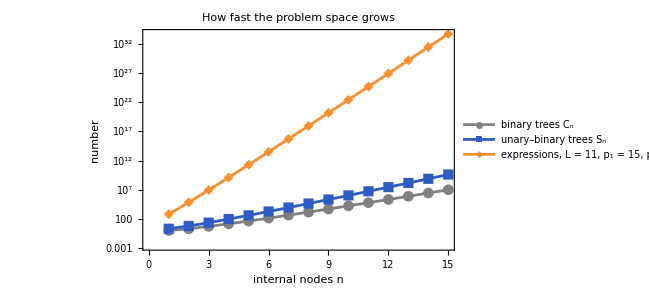

```mathematica
(* id: 2f24cbbd-18b4-4822-a378-112516bea822 · unit2_symbolic_data · cell 13 of 27 · updated 2026-11-24 06:52 UTC *)
paper = {11, 15, 4};
ListLogPlot[{Table[CatalanNumber[n], {n, 1, 15}], Table[schroeder[n], {n, 1, 15}], Table[Eexpr[n, paper], {n, 1, 15}]},
 Joined -> True, PlotMarkers -> Automatic, PlotStyle -> {GrayLevel[0.5], RGBColor[0.18, 0.36, 0.78], RGBColor[0.98, 0.56, 0.17]},
 PlotLegends -> {"binary trees Cₙ", "unary–binary trees Sₙ", "expressions, L = 11, p₁ = 15, p₂ = 4"},
 Frame -> True, FrameLabel -> {"internal nodes n", "number"}, PlotLabel -> "How fast the problem space grows", ImageSize -> 480, ImagePadding -> {{60, 10}, {40, 30}}]
```

Fig. 2. The number of trees and of expressions with n internal nodes, on a log scale. With the paper’s operators and leaves there are about 5.4 × 10.b3.b3 expressions with 15 internal nodes.

```mathematica
(* id: 321a498a-ffd4-471d-b7d7-832ef4b40eda · unit2_symbolic_data · cell 14 of 27 · updated 2026-11-24 06:52 UTC *)
{N[Eexpr[15, paper], 3], Floor[Log10[Eexpr[15, paper]]]}
```

{5.43×10^33,33}

Check: {5.43 × 10.b3.b3, 33}.

## 5. Sampling trees uniformly

A naive recursive generator (binary or unary with fixed probabilities, then a random split of the remaining nodes) favours some shapes. The paper samples every tree with n internal nodes equally often. Start with one empty slot, e = 1. Choose the position k and arity a of the next internal node with

P(k, unary) = D(e − k, n − 1) / D(e, n),     P(k, binary) = D(e − k + 1, n − 1) / D(e, n),     k = 0, …, e − 1

The k slots before it become leaves. Then e becomes e − k (unary) or e − k + 1 (binary), and n falls by 1. The tree comes out in prefix order.

### 5.1 Worked by hand: the first choice for n = 2

With e = 1 only k = 0 is possible. P(0, unary) = D(1, 1)/D(1, 2) = 2/6 = 1/3 and P(0, binary) = D(2, 1)/D(1, 2) = 4/6 = 2/3. That matches the list of §4.1: of the six trees, two start with u and four with b. A fair first choice is exactly the fraction of trees that start that way.

```mathematica
(* id: 585aa8be-b0ed-439a-9b02-73d4f95af51b · unit2_symbolic_data · cell 15 of 27 · updated 2026-11-24 06:52 UTC *)
choices[1, 2]
```

{{0,1}→2,{0,2}→4}

Check: {{0, 1} → 2, {0, 2} → 4}, weights 2 and 4 out of 6.

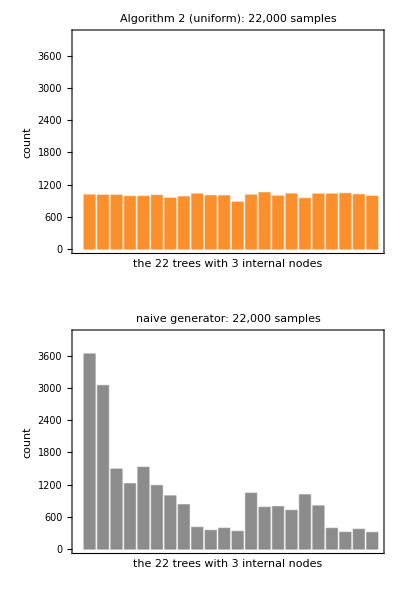

```mathematica
(* id: c1878cd0-4c60-4f4b-830e-431f5861a662 · unit2_symbolic_data · cell 16 of 27 · updated 2026-11-24 06:52 UTC *)
all3 = allTrees[3]; good = Table[randomTree[3], 22000]; naive = Table[naiveTree[3], 22000];
freq[s_] := Lookup[Counts[s], all3, 0];
Column[Table[BarChart[freq[d[[1]]], ChartStyle -> d[[2]], PlotRange -> {0, 4000}, Frame -> True,
   FrameLabel -> {"the 22 trees with 3 internal nodes", "count"}, PlotLabel -> d[[3]], ImageSize -> 480, ImagePadding -> {{60, 10}, {40, 30}}],
  {d, {{good, RGBColor[0.98, 0.56, 0.17], "Algorithm 2 (uniform): 22,000 samples"}, {naive, GrayLevel[0.55], "naive generator: 22,000 samples"}}}]]
```

Fig. 3. Counts of the 22 trees with three internal nodes in 22,000 samples. The paper’s algorithm gives each about 1000; the naive generator gives some shapes more than 3000 and others about 300.

```mathematica
(* id: 90c59d56-8e00-4f2a-9c5d-b3cf13085fb4 · unit2_symbolic_data · cell 17 of 27 · updated 2026-11-24 06:52 UTC *)
{Union[good] == Sort[all3], uniformP[good, all3] > 0.001, uniformP[naive, all3] < 10^-6, Min[freq[naive]], Max[freq[naive]]}
```

{True,True,True,314,3637}

Check: {True, True, True, …}: all 22 trees appear; the paper’s sampler is consistent with uniform (χ.b2 p-value above 0.001); the naive one is not (p below 10⁻⁶); the last two numbers are its smallest and largest counts.

```mathematica
(* id: 3d97fa36-9db6-4d3e-a241-3b87664f7087 · unit2_symbolic_data · cell 18 of 27 · updated 2026-11-24 06:52 UTC *)
b4 = Select[allTrees[4], FreeQ[#, 1] &]; s4 = Table[randomBinaryTree[4], 14000];
{Length[b4], Union[s4] == Sort[b4], uniformP[s4, b4] > 0.001}
```

{14,True,True}

Check: {14, True, True}. The binary version (Algorithm 1), used in Unit 4 for ⨂/⨁ trees, is uniform over the C₄ = 14 binary trees.

Decorating a tree chooses an operator for every node and x or an integer for every leaf. Three random expressions with four internal nodes:

```mathematica
(* id: d09fcc33-0fb2-4d70-88c1-d1300e68a1f4 · unit2_symbolic_data · cell 19 of 27 · updated 2026-11-24 06:52 UTC *)
Column[TraditionalForm /@ Table[randomExpr[4], 3]]
```

x cos(x+5)
sin(x)-cos(4)
log(log(log(log(x))))

## 6. Making integration data

Forward (FWD): draw f and ask a computer algebra system for its integral. It is slow, and it only contains integrals that system can find. Backward (BWD): draw F and differentiate; the pair (F′, F) is always available and fast. Integration by parts (IBP): if the integral of F′G is already known, the integral of FG′ follows with no computer algebra system (Section 3 of the paper).

∫ F G′ dx = F G − ∫ F′ G dx

### 6.1 Worked by hand: integration by parts

Take F = x and G = sin x, so F G′ = x cos x. The known integral needed is ∫ F′G = ∫ sin x = −cos x. So ∫ x cos x dx = x sin x − (−cos x) = x sin x + cos x. Check by differentiating: (x sin x + cos x)′ = sin x + x cos x − sin x = x cos x.

```mathematica
(* id: 7ec8f5da-7ceb-4617-a8f5-3b170129836f · unit2_symbolic_data · cell 20 of 27 · updated 2026-11-24 06:52 UTC *)
D[x Sin[x] + Cos[x], x] // Simplify
```

x Cos[x]

Check: x cos x.

### 6.2 FWD and BWD

```mathematica
(* id: 24c5a7c5-f5ac-4ed8-b644-a3853f02132f · unit2_symbolic_data · cell 21 of 27 · updated 2026-11-24 06:52 UTC *)
bwdSet = DeleteCases[Table[bwd[], 60], $Failed]; fwdSet = DeleteCases[Table[fwd[], 30], $Failed];
len[set_, i_] := N@Mean[Length[prefixOf[#[[i]]]] & /@ set];
Grid[{{"method", "pairs", "mean problem length", "mean solution length"},
  {"FWD", Length[fwdSet], NumberForm[len[fwdSet, 1], 3], NumberForm[len[fwdSet, 2], 3]},
  {"BWD", Length[bwdSet], NumberForm[len[bwdSet, 1], 3], NumberForm[len[bwdSet, 2], 3]}}, Frame -> All, Background -> {None, {LightGray}}]
```

method | pairs | mean problem length | mean solution length
FWD | 30 | 6.57 | 12.3
BWD | 60 | 8.85 | 6.78

```mathematica
(* id: 4e8d16d9-43b0-47a9-966c-1d0744acc055 · unit2_symbolic_data · cell 22 of 27 · updated 2026-11-24 06:52 UTC *)
{AllTrue[bwdSet, verifiedQ[#[[1]], prefixOf[#[[2]]]] &], AllTrue[fwdSet, verifiedQ[#[[1]], prefixOf[#[[2]]]] &], len[bwdSet, 1] > len[bwdSet, 2]}
```

{True,True,True}

Check: {True, True, True}. Every pair is correct, and BWD problems are longer than their solutions on average: differentiation lengthens expressions. The paper sees the same (its Table 1), and notes that a model trained only on BWD data learns that integrating shortens expressions, which FWD data contradicts.

### 6.3 IBP from a small table

Start with the BWD pairs of six functions, then apply integration by parts to every pair (F, G) of them, three times; each round can use what the previous one found.

```mathematica
(* id: d3180e70-059f-43a8-9588-37d66e6e4bc0 · unit2_symbolic_data · cell 23 of 27 · updated 2026-11-24 06:52 UTC *)
pool = {x, x^2, x^3, Sin[x], Cos[x], Exp[x]};
k0 = {D[#, x], #} & /@ pool;
ibp = Drop[Nest[ibpRound[#, pool] &, k0, 3], Length[k0]];
Grid[Prepend[{TraditionalForm[#[[1]]], TraditionalForm[#[[2]]]} & /@ Take[ibp, UpTo[10]], {"problem", "solution found by IBP"}], Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

problem | solution found by IBP
x cos(x) | x sin(x)+cos(x)
-x sin(x) | x cos(x)-sin(x)
x ⅇ^x | (x-1) ⅇ^x
x^2 cos(x) | (x^2-2) sin(x)+2 x cos(x)
-x^2 sin(x) | (x^2-2) cos(x)-2 x sin(x)
x^2 ⅇ^x | (x^2-2 x+2) ⅇ^x
x^3 cos(x) | x (x^2-6) sin(x)+3 (x^2-2) cos(x)
-x^3 sin(x) | x (x^2-6) cos(x)-3 (x^2-2) sin(x)
x^3 ⅇ^x | (x^3-3 x^2+6 x-6) ⅇ^x

```mathematica
(* id: 9686cc7f-abef-4fd3-b1e9-afdabef896e2 · unit2_symbolic_data · cell 24 of 27 · updated 2026-11-24 06:52 UTC *)
{Length[ibp], AllTrue[ibp, verifiedQ[#[[1]], prefixOf[#[[2]]]] &], AnyTrue[ibp, FreeQ[Quiet@Simplify[#[[1]]/(x^3 Sin[x])], x] &]}
```

{9,True,True}

Check: {n, True, True}: n new pairs, all correct, found without Integrate; among them ±x.b3 sin x, whose integral −x.b3 cos x + 3x.b2 sin x + 6x cos x − 6 sin x is the paper’s example of a solution that random generation would almost never produce.

## 7. Checking answers instead of trusting them

Nothing stops a decoder from writing an invalid prefix sequence; such hypotheses are thrown away. And an integral can be checked by differentiating it. So the paper checks every hypothesis in the beam, not only the most likely one; “beam size 10” means at least one of the ten was correct (Section 4.4). A constant of integration does not matter.

```mathematica
(* id: 3d92d586-e299-455b-b6dd-fbd36ee816c9 · unit2_symbolic_data · cell 25 of 27 · updated 2026-11-24 06:52 UTC *)
hyps = {{"add", "mul", "x", "sin", "x", "cos", "x"}, {"add", "mul", "x", "sin", "x", "add", "cos", "x", "INT+", "3"}, {"mul", "x", "sin", "x"}, {"add", "mul", "x", "sin"}};
Grid[Prepend[Transpose[{Row[#, " "] & /@ hyps, If[validQ[#], TraditionalForm[fromPrefix[#]], "invalid prefix"] & /@ hyps,
     verifiedQ[x Cos[x], #] & /@ hyps}], {"hypothesis for ∫ x cos x dx", "expression", "verified"}], Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

hypothesis for ∫ x cos x dx | expression | verified
  addmulxsinxcosx | x sin(x)+cos(x) | True
  addmulxsinxaddcosxINT+3 | x sin(x)+cos(x)+3 | True
  mulxsinx | x sin(x) | False
  addmulxsin | invalid prefix | False

```mathematica
(* id: c33c4680-f8e7-4e9a-b330-19c83ec39a82 · unit2_symbolic_data · cell 26 of 27 · updated 2026-11-24 06:52 UTC *)
verifiedQ[x Cos[x], #] & /@ hyps
```

{True,True,False,False}

Check: {True, True, False, False}. x sin x + cos x and x sin x + cos x + 3 are accepted; x sin x and the unfinished sequence are rejected.

## 8. Exercises

1. Write (x + 1).b2 in prefix notation and run the counter of §3.1 over it.

2. Compute D(1, 3) by hand from the recurrence, using D(1, 2) = 6 and D(2, 1) = 4.

3. With L = 2, p₁ = 2, p₂ = 1, compute E₃ from the corrected and the printed Equation 2. Which equals the count?

4. For n = 3, what is the probability that Algorithm 2 makes the root binary?

5. Use integration by parts, as in §6.1, to find ∫ x eˣ dx, and check it by differentiating.

Answers, computed:

```mathematica
(* id: 58c1539f-d581-44ff-b6ae-e2a99804bbf2 · unit2_symbolic_data · cell 27 of 27 · updated 2026-11-24 06:52 UTC *)
{prefixOf[(x + 1)^2], owed[prefixOf[(x + 1)^2]],
 {nTrees[1, 3], nTrees[2, 2], nTrees[0, 3]},
 {Eexpr[3, {2, 2, 1}], Eprinted[3, {2, 2, 1}], Total[weight[#, {2, 2, 1}] & /@ allTrees[3]]},
 Total[Values@Select[choices[1, 3], #[[1, 2]] == 2 &]]/nTrees[1, 3],
 {x Exp[x] - Exp[x], Simplify[D[x Exp[x] - Exp[x], x]]}}
```

{{pow,add,INT+,1,x,INT+,2},{1,2,3,2,1,0},{22,16,0},{352,356,352},8/11,{-ⅇ^x+x ⅇ^x,x ⅇ^x}}

1: pow add INT+ 1 x INT+ 2 (Wolfram orders 1 + x with the number first); the counter runs 1, 2, 3, 2, 1, 0, the digits counting as part of their integer. 2: D(1, 3) = D(1, 2) + D(2, 2) = 6 + 16 = 22. 3: the corrected value equals the count; the printed one does not. 4: D(2, 2)/D(1, 3) = 16/22 = 8/11. 5: ∫ x eˣ dx = x eˣ − eˣ, whose derivative is x eˣ.

## 9. Summary

Mathematics becomes data in three steps. Expressions are written as trees in prefix notation, which is short, needs no parentheses and can be read back with a single counter. Trees are sampled uniformly by counting how many ways each choice can be completed. Correct pairs come from differentiating (BWD) and from integration by parts (IBP), with no computer algebra system. Because an answer can be checked, the model need not be trusted: every hypothesis in the beam is verified. Counting the trees also caught a slip in the paper’s Equation 2.

Next: Unit 3 builds the transformer that learns from such data, and Unit 4 uses all of this on ⨂/⨁ expressions.

© 2026 Computational Classnotes · CC BY-NC-SA 4.0